```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching ""<Global`*>"". ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/Remove/rmnsm",
ButtonNote->"Remove::rmnsm"]

```mathematica
SetDirectory["~/Desktop/Work/code/bash/testBench"]
```

/users/home/arway/Desktop/Work/code/bash/testBench

```mathematica
FileNames["All*txt"]
```

{AllSpins.txt}

```mathematica
dat=Import["AllSpins.txt","Table"];
```

```mathematica
Length[dat]
```

36

```mathematica
nspins=(Length[dat])/4
spins=Table[{0,0,0},{i,1,nspins}];
```

9

```mathematica
Length[spins]
```

9

```mathematica
Do[spins[[i,1]]=dat[[4i-2]];
spins[[i,2]]=dat[[4i-1]];
spins[[i,3]]=dat[[4i]],{i,1,nspins}]
```

Check (the last) spin configuration against the file.

```mathematica
spins[[7]]//MatrixForm
```

(0.3091849015348685039 | -0.1070563696115259996 | 0.9449569463147376644
0.427960975619071464 | -0.8492668014293542299 | 0.3091849015348685039
-0.8492668014293542299 | -0.5169959706956662004 | 0.1070563696115259996)

Check the Byron relationship

```mathematica
tol=10^-6;
Do[Print["config",i-1," check a ",If[spins[[i,1,1]]+spins[[i,2,3]]<tol,0,"oops"], 
" check e ",
If[ spins[[i,2,2]]+spins[[i,3,1]]<tol,0,"oops"],
" check d ",
If[spins[[i,2,1]]+spins[[i,1,3]]+spins[[i,3,2]]<(1.1*tol),0,"oops"]],{i,1,nspins}]
```

config0 check a 0 check e 0 check d oops

config1 check a 0 check e 0 check d oops

config2 check a oops check e 0 check d oops

config3 check a oops check e 0 check d oops

config4 check a 0 check e 0 check d 0

config5 check a 0 check e 0 check d oops

config6 check a oops check e 0 check d oops

config7 check a oops check e 0 check d 0

config8 check a 0 check e 0 check d 0

Now let’s take a look at what θ and ϕ values Andrew’s configurations correspond to.

tan ϕ = b/a (= sinθ sinϕ / sinθ cosϕ = y/x)
ArcTan[x,y]
cosθ=c

```mathematica
theta=Table[0,{i,1,nspins}];
phi=Table[0,{i,1,nspins}];
Do[theta[[i]]=ArcCos[spins[[i,1,3]]];
phi[[i]]=ArcTan[spins[[i,1,1]],spins[[i,1,2]]],{i,1,nspins}]
```

```mathematica
Bound[ϕ_]:=If[Cos[4 ϕ]==1,π/3,ArcSin[√((4-√(16-6(1-Cos[4 ϕ])))/(1-Cos[4ϕ]))]]
```

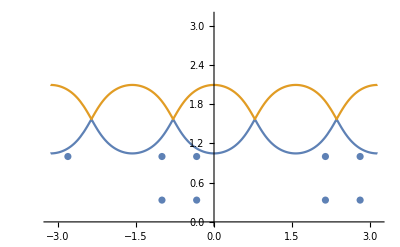

```mathematica
gsPlot=ListPlot[Transpose[{phi,theta}],Frame->{True,True,False,False},FrameLabel->{"ϕ","θ"},Axes->False,PlotRangePadding->Automatic];
boundPlot=Plot[{Bound[ϕ],π-Bound[ϕ]},{ϕ,-π,π},PlotRange->{{-180Degree,180Degree},{0,π}}];
Show[boundPlot,gsPlot]
```